# EIWL Sections 45, 46

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

## Section 45

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

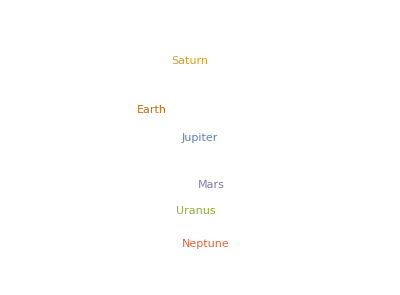

```mathematica
WordCloud[Normal[planets[All,"Moons",Length]]]
```

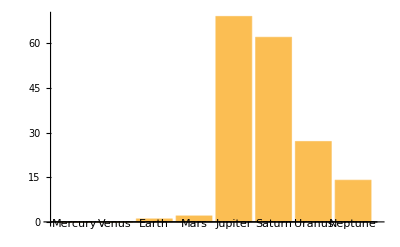

```mathematica
BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

```mathematica
SortBy[planets[All,"Mass"],planets["Moons",Length]]
```

```mathematica
planets[All,"Moons",Total,"Mass"]
```

```mathematica
planets[All,"Moons",Total,"Mass"][Sort]
```

```mathematica
planets[All,"Moons",Median,"Mass"]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[5.972*^24, "Kilograms"]&]/*Keys]
```

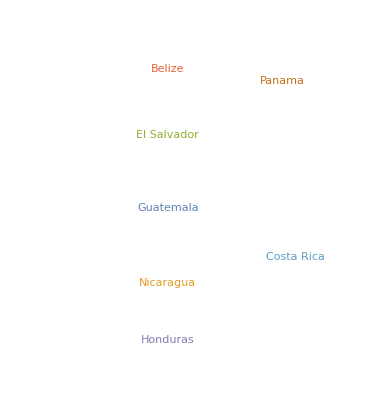

```mathematica
WordCloud[Association[#->Length[TextWords[WikipediaData[#]]]&/@EntityList[]]]
```

```mathematica
ResourceData["Fireballs and Bolides"][Max,"Altitude"]
```

66.6 km

```mathematica
TakeLargest[ResourceData["Fireballs and Bolides"][All,"Altitude"],5]
```

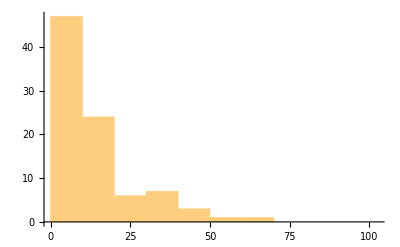

```mathematica
Histogram[Differences[Normal[ResourceData["Fireballs and Bolides"][All,"PeakBrightness"]]]]
```

```mathematica
Take[ResourceData["Fireballs and Bolides"][All,"Coordinates"],10]
```

```mathematica
GeoListPlot[GeoNearest["City",#]&/@]
```

-Graphics-

```mathematica
SortBy[ResourceData["Fireballs and Bolides"][All]"LargestAltitude"]
```

SortBy[LargestAltitude ]

```mathematica
GeoListPlot[ResourceData["Fireballs and Bolides"][TakeLargestBy[#Altitude&,10],"NearestCity"],GeoLabels->True]
```

-Graphics-

## Section 46

```mathematica
Spectrogram[SpeechSynthesize[IntegerName[123456]]]
```

-Graphics-

```mathematica
Spectrogram[SpeechSynthesize[Reverse[SortBy[WordList[],StringLength]][[1]]]]
```

-Graphics-

```mathematica
SpeechSynthesize[StringJoin[Riffle[Alphabet[]," "]]]
```

```mathematica
Spectrogram[SpeechSynthesize[StringJoin[Riffle[Alphabet[]," "]]]]
```

-Graphics-

```mathematica
AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
(*Table[SpeechRecognize[AudioPitchShift[SpeechSynthesize["computer"],x]],{x,1,1.5,0.1}]*) (*This was taking a long time to evaluate but I think it's right?*)
```

$Aborted

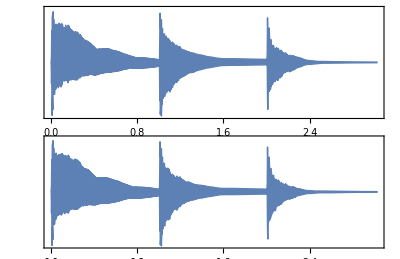

```mathematica
AudioPlot[Sound[{SoundNote[0,1,"Guitar"],SoundNote[12,1,"Guitar"],SoundNote[24,1,"Guitar"]}]]
```

```mathematica
(*Table[SpeechRecognize[AudioPitchShift[Sound[SoundNote[0,1,"Trumpet"]],x]],{x,0.5,1,0.1}]*) (*This one is also just not executing*)
```

```mathematica
AnimationVideo[Blur[-Graphics-,x],{x,20,0}]
```

```mathematica
AnimationVideo[Graphics[{Style[Disk[],Red],RegularPolygon[x]}],{x,3,20}]
```

```mathematica
Style[AnimationVideo[Graphics[Style[Disk[],Hue[x]]],{x,0,1}],50]
```

```mathematica
AnimationVideo[Rasterize[Style[ToUpperCase[FromLetterNumber[x]],50]],{x,1,26,1}]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 26/5 to 2599653/500000.